500

3.7

InterpolatingFunction::dmval: Input value {-3.6898} lies outside the range of data in the interpolating function. Extrapolation will be used.

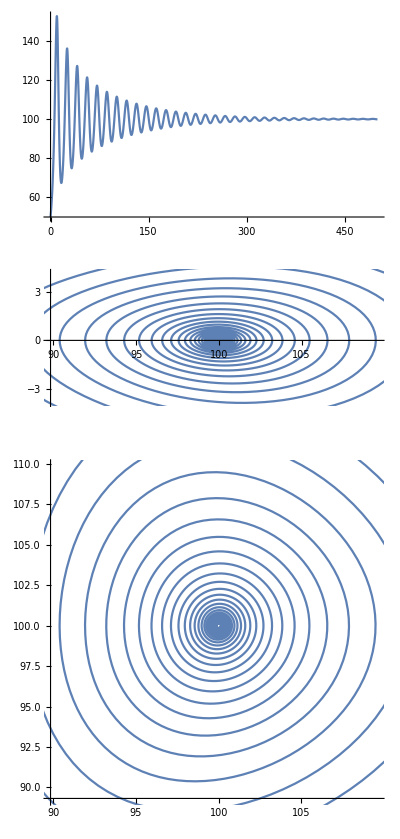

```mathematica
Remove[T,r,K,A]
r=0.1;
K=100;
A=20;
T=1;
tEnd=500
T=3.7
s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1),y[t/;t<=0]==50},y,{t,0,tEnd}];
GraphicsColumn[{
	Plot[Evaluate[y[x]/. s],{x,0,tEnd},PlotRange->All],
	ParametricPlot[Evaluate[{y[t],y'[t]}/. Flatten@{s}],{t,0,tEnd}],
	ParametricPlot[Evaluate[{y[t],y[t-T]}/. Flatten@{s}],{t,0,tEnd}]
}]

Manipulate[s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1),y[t/;t<=0]==50},y,{t,0,tEnd}];
GraphicsColumn[
		{Plot[Evaluate[y[x]/. s],{x,0,tEnd},PlotRange->All],
	ParametricPlot[Evaluate[{y[t],y'[t]}/. Flatten@{s}],{t,0,tEnd}
]}
],{T,4.4,4.6,0.01,Appearance->"Labeled"}]
(*
Manipulate[s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1),y[t/;t<=0]==50},y,{t,0,tEnd}];
Plot[Evaluate[y[x]/. s],{x,0,tEnd},PlotRange->All],
{T,0,5,0.1}]
Manipulate[s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1),y[t/;t<=0]==50},y,{t,0,tEnd}];
ParametricPlot[Evaluate[{y[t],y'[t]}/. Flatten@{s}],{t,0,tEnd}],
{T,0,5,0.1}]
(*
Manipulate[s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1),y[t/;t<=0]==50},y,{t,0,30}];
ParametricPlot[Evaluate[{y[t],y'[t]}/. Flatten@{s}],{t,0,10}],{T,0,5,0.1}]
Manipulate[s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1),y[t/;t<=0]==50},y,{t,0,30}];
ParametricPlot[Evaluate[{y[t],y[t-T]}/. Flatten@{s}],{t,0,10}],{T,0,5,0.1}]

Manipulate[s=NDSolve[{y'[t]==r*y[t]*(1-y[t-T]/K)*(y[t]/A-1),y[t/;t<=0]==50},y,{t,0,30}];
		Plot[Evaluate[y[x]/. s],{x,0,30},PlotRange->All],
	ParametricPlot[Evaluate[{y[t],y'[t]}/. Flatten@{s}],{t,0,30}],{T,0,5,0.1}]
```